```mathematica
a=Import["/home/jirka/Desktop/2565b.png","Graphics"];
c=ImageCrop[a,{500,500},Bottom, Padding->Transparent]
```

-Graphics-

```mathematica
Rectangle[{0,5},{2,40},a]
```

Rectangle[{0,5},{2,40},$Failed]

```mathematica
imgs={ExampleData[{"TestImage","Clock"}],ExampleData[{"TestImage","Elaine"}],ExampleData[{"TestImage","JellyBeans"}],ExampleData[{"TestImage","Lena"}],ExampleData[{"TestImage","Mandrill"}],ExampleData[{"TestImage","Peppers"}],ExampleData[{"TestImage","Splash"}],ExampleData[{"TestImage","Tiffany"}],ExampleData[{"TestImage","U2"}]};
```

```mathematica
place[img_,{x_,y_},r_]:=Module[{w,h},{w,h}=ImageDimensions[img];Graphics[Rectangle[{x,y},{x+w*r,y+h*r},img]]]
```

ImageDimensions::imginv: Expecting an image or graphics instead of ImageRotate[$Failed, 30\ °].

Set::shape: Lists {w$6014, h$6014} and ImageDimensions[ImageRotate[$Failed, 30\ °]] are not the same shape.

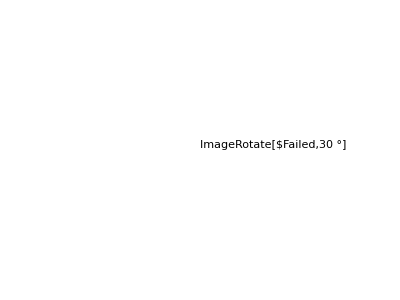

```mathematica
place[b,{500,20},.5]
```

```mathematica
Show[place[a,{0,100},1], place[b,{0,150},0.5],Background->Transparent]
```

ImageDimensions::imginv: Expecting an image or graphics instead of $Failed.

Set::shape: Lists {w$6028, h$6028} and ImageDimensions[$Failed] are not the same shape.

ImageDimensions::imginv: Expecting an image or graphics instead of ImageRotate[$Failed, 30\ °].

Set::shape: Lists {w$6033, h$6033} and ImageDimensions[ImageRotate[$Failed, 30\ °]] are not the same shape.

-Graphics-

```mathematica
d[img_]:=Module[{w,h},{w,h}=ImageDimensions[img];Show[{place[ImageRotate[img,45 Degree, Background->Transparent],{w*0.35,h*0.20},0.6], place[ImageRotate[img,-45Degree, Background->Transparent],{w*0.65,h*0.20},0.6],place[c,{w*0.45,0},1]},Background->Transparent]]

d[c]
d[%]
```

-Graphics-

-Graphics-

```mathematica
c
```

-Graphics-

```mathematica
f=NestList[d,a,3]
```

ImageDimensions::imginv: Expecting an image or graphics instead of $Failed.

Set::shape: Lists {w$6172, h$6172} and ImageDimensions[$Failed] are not the same shape.

ImageRotate::imginv: Expecting an image or graphics instead of $Failed.

ImageDimensions::imginv: Expecting an image or graphics instead of ImageRotate[$Failed, 45\ °, Background → GrayLevel[0, 0]].

Set::shape: Lists {w$6179, h$6179} and ImageDimensions[ImageRotate[$Failed, 45\ °, Background → GrayLevel[0, 0]]] are not the same shape.

ImageRotate::imginv: Expecting an image or graphics instead of $Failed.

ImageDimensions::imginv: Expecting an image or graphics instead of ImageRotate[$Failed, -45\ °, Background → GrayLevel[0, 0]].

General::stop: Further output of ImageDimensions :: imginv will be suppressed during this calculation.

Set::shape: Lists {w$6186, h$6186} and ImageDimensions[ImageRotate[$Failed, -45\ °, Background → GrayLevel[0, 0]]] are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

{$Failed,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[Reverse[f]]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[{-Graphics-,-Graphics-,-Graphics-,$Failed}]

ImageRotate::imginv: Expecting an image or graphics instead of $Failed.

ImageDimensions::imginv: Expecting an image or graphics instead of ImageRotate[$Failed, 1/GoldenRatio, Background → GrayLevel[0, 0]].

Set::shape: Lists {w$6389, h$6389} and ImageDimensions[ImageRotate[$Failed, 1/GoldenRatio, Background → GrayLevel[0, 0]]] are not the same shape.

ImageRotate::imginv: Expecting an image or graphics instead of $Failed.

ImageDimensions::imginv: Expecting an image or graphics instead of ImageRotate[$Failed, -1/GoldenRatio, Background → GrayLevel[0, 0]].

Set::shape: Lists {w$6396, h$6396} and ImageDimensions[ImageRotate[$Failed, -1/GoldenRatio, Background → GrayLevel[0, 0]]] are not the same shape.

ImageRotate::imginv: Expecting an image or graphics instead of $Failed.

ImageDimensions::imginv: Expecting an image or graphics instead of ImageRotate[$Failed, 1/GoldenRatio, Background → GrayLevel[0, 0]].

Set::shape: Lists {w$6403, h$6403} and ImageDimensions[ImageRotate[$Failed, 1/GoldenRatio, Background → GrayLevel[0, 0]]] are not the same shape.

ImageRotate::imginv: Expecting an image or graphics instead of $Failed.

ImageDimensions::imginv: Expecting an image or graphics instead of ImageRotate[$Failed, -1/GoldenRatio, Background → GrayLevel[0, 0]].

Set::shape: Lists {w$6410, h$6410} and ImageDimensions[ImageRotate[$Failed, -1/GoldenRatio, Background → GrayLevel[0, 0]]] are not the same shape.

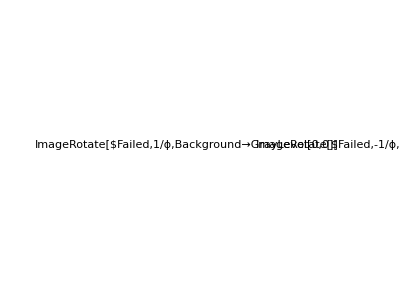
{$Failed,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
d[img_]:=Show[place[ImageRotate[img,1/GoldenRatio, Background->Transparent],{190,190},1/GoldenRatio], place[ImageRotate[img,-1/GoldenRatio, Background->Transparent],{360,190},1/GoldenRatio]]
e=d[a];
NestList[d,a,5]
```

```mathematica
Show[Reverse[%]]
```

-Graphics-

```mathematica
ImageRotate[a,80 Degree,Background->Transparent]
place[a,{0,0},1]
```

-Graphics-

-Graphics-

```mathematica
Show
```

```mathematica
d[img_,l_]:=If[l>0,Module[{w,h},{w,h}=ImageDimensions[img];Show[{place[ImageRotate[d[img,l-1],45 Degree, Background->Transparent],{w*0.40,h*0.45},1/GoldenRatio], place[ImageRotate[d[img,l-1],-45Degree, Background->Transparent],{w*0.60,h*0.45},1/GoldenRatio]},Background->Transparent]],Show[Graphics@Rectangle[], Background->Transparent]]
```

```mathematica
d[c,3]
```

-Graphics-